```mathematica
Needs["PlotLegends`"];
Needs["PlotLegends`"];
```

## Parameters

```mathematica
c=2.997924 10^8 ;     (* Speed of light, [m/s] *)
mpc=3.085678 10^22; (* Megaparsec [m] *)
pc=3.086 10^16;
G=6.67428 10^(-11); (* Gravitational constant, [m^3/kg/s^2] *)
Gsurc4=6.708 10^(-57); (* G/c^4 in [ev^-2] *)
msun=2 10.^30; (* Sun mass [kg]*)
year=365.25 24 3600; (* [s] *)
hbar=6.62607 10^(-34)/(2 Pi); (*in m^2 kg /s*)
invsecondinkg=hbar /c^2;
(* Cosmo parameters *)
h=0.7 ;
H0=h 100000 /mpc;  (* Hubble rate today, [s^-1] *) 
rhocr := 3 H0^2 / (8 Pi G ); (* Critical Density [kg/m^3] *)
ar=7.5657 10^(-16); (* Stephan's constant in J m^-3 K^-4 *);
T0=2.726 (* en K *);
Subscript[Ω, b]=0.0456;
Subscript[Ω, CDM]=0.245;
Subscript[Ω, r]=ar  T0^4/rhocr /c^2;
Nur=3.046;
Subscript[Ω, ν]=Subscript[Ω, r] 7./8 Nur(4/11)^(4/3);
Subscript[Ω, Λ]=1-(Subscript[Ω, CDM]+Subscript[Ω, b]+Subscript[Ω, r]+Subscript[Ω, ν]);
AU=1.4960 10^11;
VolumeGpc=10.^27;
eps0=13.605698 ;(* en eV *);
kb=8.617343 10^(-5); (* en eV /K *);
eVinJ = 1.60217 10^(-19);
hp=6.582 10^(-16); (* Planck constant in eV s *)
me=510998; (* electron mass in eV *)
mh=938.272 10^6;(* proton mass in eV *)
mproton=1.67 10^(-27)(* proton mass in kg *)
Omr=ar  T0^4/rhocr /c^2;
sigmaT=6.652462 10^(-29); (* Thomson cross section in m^2 *)
fHe=0.24 ;(* helium fraction*)
eVenJ=1.6022 10^(-19); (* eV en J *)
T21= 0.068  ;         (* 21cm transition temperature in kelvin *)
lambda21=0.21;
A10=2.869 10^(-15);    (* Enstein coefficient of spontaneous emission in s^-1 *)
lplanck=1.61 10^(-35);
azero=3.70 10^-7;
rhoplanck=5.155 10^96;
mplanck=1.22 10^19;
```

1.67×10^-27

## Background cosmology

```mathematica
Subscript[ρ, CDM][a_] := Subscript[Ω, CDM] rhocr / a^3 ;
Subscript[ρ, b][a_] := Subscript[Ω, b] rhocr / a^3 ;
H[a_]:=H0 Sqrt[(Subscript[Ω, CDM]+Subscript[Ω, b])/a^3+(Subscript[Ω, r]+Subscript[Ω, ν])/a^4+Subscript[Ω, Λ]];
aa[z_]:= 1/(z+1);
HMass[a_]:=(3 H[a]^2 /(8 Pi G ))( H[a]/c)^-3;
T[a_]=((3 H[a]^2 /(8 Pi G ))/(rhoplanck))^(1/4)mplanck 10^3 ;
kk[a_]=a H[a]/c mpc;
HmassofT[logTinMeV_]:=4π 10^rhoQCDbis[logTinMeV](((10^rhoQCDbis[logTinMeV]) 8π G/3)^(1/2)/c)^-3/3;

(*Trad[a_]=(*(kb T0/10^9/a)10^3 *)((Subscript[Ω, r]+Subscript[Ω, ν])rhocr/a^4 /rhoplanck)^(1/4)mplanck 10^3 *)
```

## Thermal history

### Thermal history from arXiv:

```mathematica
wofTdata={{0.01045504,0.33325583},{0.012644596,0.33325505},{0.038893126,0.33314726},{0.042299554,0.33299232},{0.045215935,0.33283746},{0.048572592,0.33247644},{0.052178357,0.33196086},{0.055091128,0.33129072},{0.05831023,0.33046603},{0.061717276,0.32938367},{0.06548471,0.3279921},{0.06896908,0.3262914},{0.07210281,0.32474533},{0.07650349,0.3223747},{0.081978455,0.319901},{0.089596525,0.31582975},{0.09413051,0.3134592},{0.102119125,0.31000635},{0.11024067,0.30727494},{0.11754822,0.30495584},{0.12596135,0.303152},{0.1333209,0.301812},{0.14321749,0.3009872},{0.15233728,0.30067778},{0.16004981,0.30062604},{0.16940357,0.3008319},{0.1788622,0.30129546},{0.18931617,0.3019136},{0.19792241,0.3026348},{0.20539272,0.3034076},{0.21632649,0.3041288},{0.22616117,0.30510768},{0.23820144,0.30624112},{0.24903086,0.30732307},{0.26035234,0.30830193},{0.27017927,0.3091778},{0.28176543,0.31010514},{0.29676625,0.31134164},{0.31179446,0.3124751},{0.3243637,0.31355706},{0.3382736,0.31453595},{0.3545267,0.3155148},{0.37524995,0.31675127},{0.40013832,0.3180908},{0.42352754,0.31927574},{0.44828367,0.32040915},{0.4780148,0.321491},{0.5160511,0.3227274},{0.551637,0.3237577},{0.5970031,0.3248395},{0.6525143,0.32602432},{0.7026952,0.32679695},{0.7623633,0.32772416},{0.8291426,0.3285998},{0.8995455,0.32926935},{0.985616,0.33014497},{1.0799203,0.330866},{1.1832471,0.33153552},{1.2837154,0.33205047},{1.3756211,0.33235937},{1.5641131,0.33271953},{1.73077,0.33282217},{1.87309,0.33297643},{7.864243,0.33302194},{8.745254,0.33296996},{9.700971,0.33286646},{10.655334,0.33250535},{11.732517,0.3320927},{12.760057,0.33157706},{13.877542,0.3307007},{15.2803545,0.32951513},{16.577463,0.3279689},{17.851936,0.3264227},{19.704857,0.32394883},{22.18379,0.3202382},{28.819191,0.31199232},{31.034637,0.3098793},{33.173935,0.3084362},{35.112278,0.30735382},{38.187164,0.30611676},{41.634277,0.30554956},{44.83583,0.30565232},{48.045837,0.30606425},{51.485764,0.30668232},{56.13403,0.3074034},{60.153137,0.30817604},{65.09981,0.30884558},{68.904495,0.30915454},{74.020035,0.3092573},{80.30431,0.30889624},{85.20692,0.30817458},{89.51992,0.30714378},{94.98429,0.30549458},{100.53299,0.30317548},{104.32484,0.30132025},{108.79537,0.29915583},{112.06517,0.29693994},{115.43289,0.29441485},{118.90135,0.29147753},{121.56999,0.28848872},{126.776695,0.28400543},{128.03255,0.2818927},{130.90523,0.27818245},{135.1693,0.2731839},{139.91449,0.26607266},{144.47008,0.25968283},{148.0753,0.254942},{152.14334,0.24855217},{157.0978,0.24262612},{160.62238,0.23876129},{165.44742,0.23505102},{169.99904,0.23252594},{176.41176,0.23113449},{181.2688,0.23077367},{186.26094,0.2311858},{190.44832,0.23195864},{192.81612,0.23288614},{198.12766,0.23401967},{201.58566,0.23577161},{206.1195,0.23752353},{210.75636,0.23979075},{215.49712,0.24185185},{219.80235,0.24453132},{225.86032,0.24705616},{232.66139,0.2506116},{239.66618,0.25370327},{245.05807,0.25612506},{250.57164,0.25870144},{258.1149,0.26148394},{267.86267,0.264421},{277.29205,0.26699734},{284.23087,0.269213},{296.424,0.27168626},{309.90442,0.27410796},{326.40833,0.2769419},{349.7882,0.2805487},{371.15485,0.28317645},{394.8014,0.28606185},{413.77457,0.28807133},{436.88434,0.29013228},{454.49854,0.29172954},{477.516,0.2932237},{499.22763,0.2947694},{520.6387,0.29621208},{552.437,0.29796383},{590.5352,0.29956096},{626.60187,0.3012097},{676.4642,0.30285832},{721.33234,0.30445546},{782.588,0.30605254},{857.4741,0.3077011},{934.8979,0.30940124},{1024.357,0.31089523},{1119.6094,0.31249228},{1223.7178,0.31398627},{1337.5049,0.31532568},{1447.5021,0.31656206},{1543.5043,0.31769544},{1645.8688,0.31851965},{1763.7139,0.31949842},{1880.6833,0.32037416},{2015.3423,0.32140446},{2213.6387,0.3224862},{2401.6047,0.32336184},{2631.401,0.3244436},{2977.2485,0.32567978},{3335.4414,0.32691604},{3755.2256,0.32804918},{4280.361,0.3290277},{4988.574,0.32990307},{5452.3926,0.330418},{6003.6406,0.33082983},{6826.2783,0.33119},{7666.381,0.33139563},{8588.621,0.33139515},{9503.733,0.33139473},{10913.188,0.3313426},{12562.62,0.3309813},{14354.569,0.33031088},{16200.857,0.329692},{17926.914,0.32891864},{20789.693,0.32773283},{23696.432,0.32644403},{26876.512,0.32515526},{30408.193,0.323918},{34488.98,0.32257771},{39021.168,0.32185578},{44477.227,0.32118535},{49704.676,0.32092723},{54729.703,0.32092685},{61617.105,0.32097787},{67679.29,0.32123512},{72883.805,0.32159552},{81450.5,0.32211035},{93762.195,0.3230373},{105823.695,0.32417044},{120920.695,0.32535508},{151019.12,0.32777604},{183101.48,0.32973337},{210259.47,0.33117563},{244444.36,0.33225712},{277254.1,0.33287492},{292011.8,0.33308083},{308315.5,0.33328673},{2975169.5,0.33327723}};
```

```mathematica
TableForm[%4]
```

0.010455 | 0.333256
0.0126446 | 0.333255
0.0388931 | 0.333147
0.0422996 | 0.332992
0.0452159 | 0.332837
0.0485726 | 0.332476
0.0521784 | 0.331961
0.0550911 | 0.331291
0.0583102 | 0.330466
0.0617173 | 0.329384
0.0654847 | 0.327992
0.0689691 | 0.326291
0.0721028 | 0.324745
0.0765035 | 0.322375
0.0819785 | 0.319901
0.0895965 | 0.31583
0.0941305 | 0.313459
0.102119 | 0.310006
0.110241 | 0.307275
0.117548 | 0.304956
0.125961 | 0.303152
0.133321 | 0.301812
0.143217 | 0.300987
0.152337 | 0.300678
0.16005 | 0.300626
0.169404 | 0.300832
0.178862 | 0.301295
0.189316 | 0.301914
0.197922 | 0.302635
0.205393 | 0.303408
0.216326 | 0.304129
0.226161 | 0.305108
0.238201 | 0.306241
0.249031 | 0.307323
0.260352 | 0.308302
0.270179 | 0.309178
0.281765 | 0.310105
0.296766 | 0.311342
0.311794 | 0.312475
0.324364 | 0.313557
0.338274 | 0.314536
0.354527 | 0.315515
0.37525 | 0.316751
0.400138 | 0.318091
0.423528 | 0.319276
0.448284 | 0.320409
0.478015 | 0.321491
0.516051 | 0.322727
0.551637 | 0.323758
0.597003 | 0.32484
0.652514 | 0.326024
0.702695 | 0.326797
0.762363 | 0.327724
0.829143 | 0.3286
0.899546 | 0.329269
0.985616 | 0.330145
1.07992 | 0.330866
1.18325 | 0.331536
1.28372 | 0.33205
1.37562 | 0.332359
1.56411 | 0.33272
1.73077 | 0.332822
1.87309 | 0.332976
7.86424 | 0.333022
8.74525 | 0.33297
9.70097 | 0.332866
10.6553 | 0.332505
11.7325 | 0.332093
12.7601 | 0.331577
13.8775 | 0.330701
15.2804 | 0.329515
16.5775 | 0.327969
17.8519 | 0.326423
19.7049 | 0.323949
22.1838 | 0.320238
28.8192 | 0.311992
31.0346 | 0.309879
33.1739 | 0.308436
35.1123 | 0.307354
38.1872 | 0.306117
41.6343 | 0.30555
44.8358 | 0.305652
48.0458 | 0.306064
51.4858 | 0.306682
56.134 | 0.307403
60.1531 | 0.308176
65.0998 | 0.308846
68.9045 | 0.309155
74.02 | 0.309257
80.3043 | 0.308896
85.2069 | 0.308175
89.5199 | 0.307144
94.9843 | 0.305495
100.533 | 0.303175
104.325 | 0.30132
108.795 | 0.299156
112.065 | 0.29694
115.433 | 0.294415
118.901 | 0.291478
121.57 | 0.288489
126.777 | 0.284005
128.033 | 0.281893
130.905 | 0.278182
135.169 | 0.273184
139.914 | 0.266073
144.47 | 0.259683
148.075 | 0.254942
152.143 | 0.248552
157.098 | 0.242626
160.622 | 0.238761
165.447 | 0.235051
169.999 | 0.232526
176.412 | 0.231134
181.269 | 0.230774
186.261 | 0.231186
190.448 | 0.231959
192.816 | 0.232886
198.128 | 0.23402
201.586 | 0.235772
206.12 | 0.237524
210.756 | 0.239791
215.497 | 0.241852
219.802 | 0.244531
225.86 | 0.247056
232.661 | 0.250612
239.666 | 0.253703
245.058 | 0.256125
250.572 | 0.258701
258.115 | 0.261484
267.863 | 0.264421
277.292 | 0.266997
284.231 | 0.269213
296.424 | 0.271686
309.904 | 0.274108
326.408 | 0.276942
349.788 | 0.280549
371.155 | 0.283176
394.801 | 0.286062
413.775 | 0.288071
436.884 | 0.290132
454.499 | 0.29173
477.516 | 0.293224
499.228 | 0.294769
520.639 | 0.296212
552.437 | 0.297964
590.535 | 0.299561
626.602 | 0.30121
676.464 | 0.302858
721.332 | 0.304455
782.588 | 0.306053
857.474 | 0.307701
934.898 | 0.309401
1024.36 | 0.310895
1119.61 | 0.312492
1223.72 | 0.313986
1337.5 | 0.315326
1447.5 | 0.316562
1543.5 | 0.317695
1645.87 | 0.31852
1763.71 | 0.319498
1880.68 | 0.320374
2015.34 | 0.321404
2213.64 | 0.322486
2401.6 | 0.323362
2631.4 | 0.324444
2977.25 | 0.32568
3335.44 | 0.326916
3755.23 | 0.328049
4280.36 | 0.329028
4988.57 | 0.329903
5452.39 | 0.330418
6003.64 | 0.33083
6826.28 | 0.33119
7666.38 | 0.331396
8588.62 | 0.331395
9503.73 | 0.331395
10913.2 | 0.331343
12562.6 | 0.330981
14354.6 | 0.330311
16200.9 | 0.329692
17926.9 | 0.328919
20789.7 | 0.327733
23696.4 | 0.326444
26876.5 | 0.325155
30408.2 | 0.323918
34489. | 0.322578
39021.2 | 0.321856
44477.2 | 0.321185
49704.7 | 0.320927
54729.7 | 0.320927
61617.1 | 0.320978
67679.3 | 0.321235
72883.8 | 0.321596
81450.5 | 0.32211
93762.2 | 0.323037
105824. | 0.32417
120921. | 0.325355
151019. | 0.327776
183101. | 0.329733
210259. | 0.331176
244444. | 0.332257
277254. | 0.332875
292012. | 0.333081
308316. | 0.333287
2.97517×10^6 | 0.333277

```mathematica
Export["wofdata.txt", txt]
```

wofdata.txt

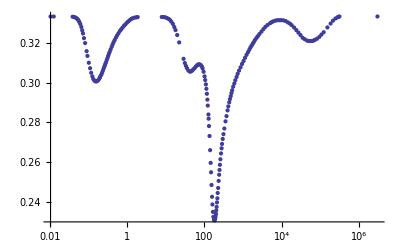

```mathematica
ListLogLinearPlot[wofTdata,PlotRange-> Full]
```

### Thermal history from arXiv:

```mathematica
prepaforspline=
{{0.,10.71,1.0},
{0.5,10.71,1.0},
{1.,10.71,1.0},
{1.5,10.71,1.0},
{2.,10.71,1.0},
{2.5,10.71,1.0},
{0.+3.,10.71,1.00228},
{0.5+3.,10.74,1.00029},
{1.+3.,10.76,1.00048},
{1.25+3.,11.09,1.00505},
{1.60+3.,13.68,1.02159},
{2.0+3.,17.61,1.02324},
{2.15+3.,24.07,1.05423},
{2.20+3.,29.84,1.07578},
{2.40+3.,47.83,1.06118},
{2.50+3.,53.04,1.04690},
{3.00+3.,73.48,1.01778},
{4.00+3.,83.10,1.00123},
{4.30+3.,85.56,1.00389},
{4.60+3.,91.97,1.00887},
{5.00+3.,102.17,1.00750},
{5.45+3.,104.98,1.00023}};
(*prepaforspline[[All,3]]=prepaforspline[[All,3]]-1.;*)
```

```mathematica
secondmethodlist=Table[{prepaforspline[[ii,1]]-3.,4./(3.prepaforspline[[ii,3]])-1.},{ii,1,Length[prepaforspline]}];
rholist=Table[{prepaforspline[[ii,1]]-3.,Log[10,prepaforspline[[ii,2]](π^2/30.)( 10^(prepaforspline[[ii,1]]-3.-3.))^4/mplanck^4 rhoplanck]},{ii,1,Length[prepaforspline]}];
rhoGeV4list=Table[{prepaforspline[[ii,1]]-3.,Log[10,prepaforspline[[ii,2]](π^2/30.)( 10^(prepaforspline[[ii,1]]-3.-3.))^4]},{ii,1,Length[prepaforspline]}];
```

```mathematica
wQCDbis= Interpolation[wofTdata,InterpolationOrder->1];
rhoQCDbis= Interpolation[rholist,Method->"Spline"];
rhoGeV4QCDbis= Interpolation[rhoGeV4list,Method->"Spline"];
wofM=Table[{HMass[10.^loga]/msun,wQCDbis[T[10^loga]]},{loga,-16.,-7.7,0.01}];
wofT=Table[{10^logT,wQCDbis[10.^logT]},{logT,-2,4,0.01}];
wofMtest=Table[{HmassofT[logT]/msun,wQCDbis[10.^logT]},{logT,-2,4,0.01}];
wofPBHmass=Interpolation[wofM,InterpolationOrder-> 3]
wofTinMeV=Interpolation[wofT,InterpolationOrder-> 3]
wofPBHmasstest=Interpolation[wofMtest,InterpolationOrder-> 3]
```

InterpolatingFunction[{{1.149×10^-8,4.57411×10^8}},<>]

InterpolatingFunction[{{0.01,10000.}},<>]

InterpolatingFunction[{{0.00053512,1.49059×10^9}},<>]

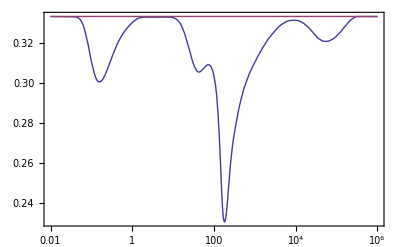

```mathematica
LogLinearPlot[{wQCDbis[T],1/3.},{T,0.01,10^6},PlotRange-> Full,Frame-> True]
```

### Critical threashofd as a function of w, from arXiv:

```mathematica
deltaMusco={
{0.0261692,0.0992309},
{0.0494427,0.170308},
{0.0756421,0.226643},
{0.0999073,0.269571},
{0.132917,0.315192},
{0.168846,0.355455},
{0.202843,0.378288},
{0.251411,0.411866},
{0.301926,0.438743},
{0.333986,0.453531},
{0.371878,0.465646},
{0.400053,0.476408}};
deltaofwMusco=Interpolation[deltaMusco];
deltaofmPBHMusco[mPBH_]=deltaofwMusco[wofPBHmasstest[mPBH]];
```

```mathematica
zetacr[mPBH_]=9/4deltaofmPBHMusco[mPBH];
turnaroundcorrectiontomass[mPBH_]:=(1+deltaofmPBHMusco[mPBH])/deltaofmPBHMusco[mPBH];
```

```mathematica
LogLinearPlot[{wofPBHmass[mPBH],1/3},{mPBH,10^-9,10^8},PlotRange-> {0.,0.4},Frame-> True]
```

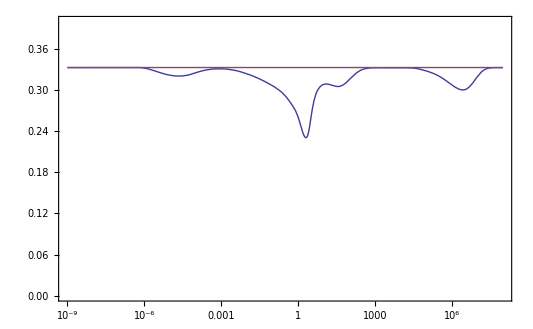
```mathematica
ga-Graphics-
```

## PBH mass functions

1.01684

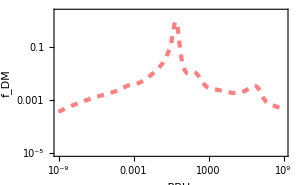

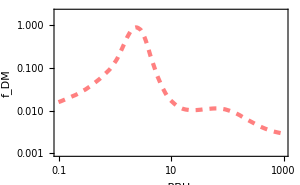

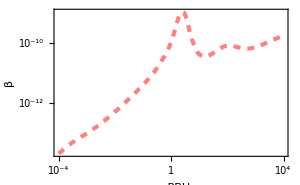

```mathematica
gamma=1.;
Amplitude=2.20 10^-2;
Subscript[n, s]=0.96;
sigmasq[mPBH_]=Amplitude (mPBH/1.)^(-(Subscript[n, s]-1)/2);
betaM0a[mPBH_]= Erfc[zetacr[mPBH]/Sqrt[2 sigmasq[mPBH]]]/2.;
MHeq=2.8 10^17;
betaeq[mPBH_]=(MHeq/mPBH)^(1/2)betaM0a[gamma mPBH];
fofmPBHM0a[mPBH_]=betaeq[mPBH]2/(Subscript[Ω, CDM]/(Subscript[Ω, CDM]+Subscript[Ω, b]));
fDMtot=NIntegrate[betaeq[mPBH]/mPBH,{mPBH,10^-9,10^7}]2/(Subscript[Ω, CDM]/(Subscript[Ω, CDM]+Subscript[Ω, b]))
PlotfDMlargeM0a=LogLogPlot[fofmPBHM0a[mPBH],{mPBH,10^-9,10^9},Frame-> True,PlotRange-> {10^-5,2.},FrameLabel->{"m_PBH","f_DM"},PlotStyle-> {Pink,Dashed,Thickness[0.01]},ImageSize-> 300]
PlotfDMzoomM0a=LogLogPlot[fofmPBHM0a[mPBH],{mPBH,10^-1,10^3},Frame-> True,PlotRange-> {0.001,2.},FrameLabel->{"m_PBH","f_DM"},PlotStyle-> {Pink,Dashed,Thickness[0.01]},ImageSize-> 300]
PlotbetaformM0a=LogLogPlot[betaM0a[mPBH],{mPBH,10^-4,10^4},Frame-> True,FrameLabel->{"m_PBH","β"},PlotStyle-> {Pink,Dashed,Thickness[0.01]},ImageSize-> 300]
```

```mathematica
(*gamma=1.;
Amplitude=2.12 10^-2;
Subscript[n, s]=0.98;
sigmasq[mPBH_]=Amplitude (mPBH/1.)^(-(Subscript[n, s]-1)/2);
betaM0b[mPBH_]= Erfc[zetacr[mPBH]/Sqrt[2 sigmasq[mPBH]]]/2.;
MHeq=2.8 10^17;
betaeq[mPBH_]=(MHeq/mPBH)^(1/2)betaM0b[gamma mPBH];
fofmPBHM0b[mPBH_]=betaeq[mPBH]2/(Subscript[Ω, CDM]/(Subscript[Ω, CDM]+Subscript[Ω, b]));
fDMtot=NIntegrate[betaeq[mPBH]/mPBH,{mPBH,10^-9,10^7}]2/(Subscript[Ω, CDM]/(Subscript[Ω, CDM]+Subscript[Ω, b]))
PlotfDMlargeM0b=LogLogPlot[fofmPBHM0b[mPBH],{mPBH,10^-9,10^9},Frame-> True,PlotRange-> {10^-5,2.},FrameLabel->{"m_PBH","f_DM"},PlotStyle-> {Pink,Dashed,Thickness[0.01]},ImageSize-> 300]
PlotfDMzoomM0b=LogLogPlot[fofmPBHM0b[mPBH],{mPBH,10^-1,10^3},Frame-> True,PlotRange-> {0.001,2.},FrameLabel->{"m_PBH","f_DM"},PlotStyle-> {Pink,Dashed,Thickness[0.01]},ImageSize-> 300]
PlotbetaformM0b=LogLogPlot[betaM0b[mPBH],{mPBH,10^-4,10^4},Frame-> True,FrameLabel->{"m_PBH","β"},PlotStyle-> {Pink,Dashed,Thickness[0.01]},ImageSize-> 300]*)
```

0.992557

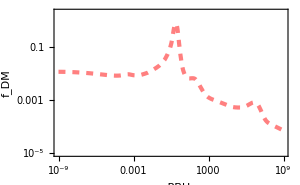

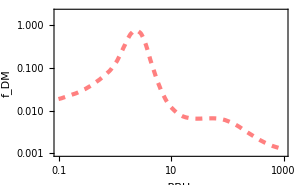

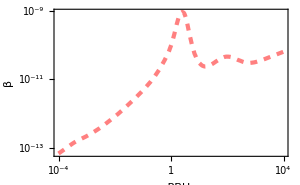

```mathematica
gamma=1.;
Amplitude=2.19 10^-2;
Subscript[n, s]=0.97;
sigmasq[mPBH_]=Amplitude (mPBH/1.)^(-(Subscript[n, s]-1)/2);
betaM0b[mPBH_]= Erfc[zetacr[mPBH]/Sqrt[2 sigmasq[mPBH]]]/2.;
MHeq=2.8 10^17;
betaeq[mPBH_]=(MHeq/mPBH)^(1/2)betaM0b[gamma mPBH];
fofmPBHM0b[mPBH_]=betaeq[mPBH]2/(Subscript[Ω, CDM]/(Subscript[Ω, CDM]+Subscript[Ω, b]));
fDMtot=NIntegrate[betaeq[mPBH]/mPBH,{mPBH,10^-9,10^7}]2/(Subscript[Ω, CDM]/(Subscript[Ω, CDM]+Subscript[Ω, b]))
PlotfDMlargeM0b=LogLogPlot[fofmPBHM0b[mPBH],{mPBH,10^-9,10^9},Frame-> True,PlotRange-> {10^-5,2.},FrameLabel->{"m_PBH","f_DM"},PlotStyle-> {Pink,Dashed,Thickness[0.01]},ImageSize-> 300]
PlotfDMzoomM0b=LogLogPlot[fofmPBHM0b[mPBH],{mPBH,10^-1,10^3},Frame-> True,PlotRange-> {0.001,2.},FrameLabel->{"m_PBH","f_DM"},PlotStyle-> {Pink,Dashed,Thickness[0.01]},ImageSize-> 300]
PlotbetaformM0b=LogLogPlot[betaM0b[mPBH],{mPBH,10^-4,10^4},Frame-> True,FrameLabel->{"m_PBH","β"},PlotStyle-> {Pink,Dashed,Thickness[0.01]},ImageSize-> 300]
```

```mathematica
(*gamma=1.;
Amplitude=2.17 10^-2;
Subscript[n, s]=0.94;
sigmasq[mPBH_]=Amplitude (mPBH/1.)^(-(Subscript[n, s]-1)/2);
betaM0c[mPBH_]= Erfc[zetacr[mPBH]/Sqrt[2 sigmasq[mPBH]]]/2.;
MHeq=2.8 10^17;
betaeq[mPBH_]=(MHeq/mPBH)^(1/2)betaM0c[gamma mPBH];
fofmPBHM0c[mPBH_]=betaeq[mPBH]2/(Subscript[Ω, CDM]/(Subscript[Ω, CDM]+Subscript[Ω, b]));
fDMtot=NIntegrate[betaeq[mPBH]/mPBH,{mPBH,10^-9,10^7}]2/(Subscript[Ω, CDM]/(Subscript[Ω, CDM]+Subscript[Ω, b]))
PlotfDMlargeM0c=LogLogPlot[fofmPBHM0c[mPBH],{mPBH,10^-9,10^9},Frame-> True,PlotRange-> {10^-5,2.},FrameLabel->{"m_PBH","f_DM"},PlotStyle-> {Pink,Dashed,Thickness[0.01]},ImageSize-> 300]
PlotfDMzoomM0c=LogLogPlot[fofmPBHM0c[mPBH],{mPBH,10^-1,10^3},Frame-> True,PlotRange-> {0.001,2.},FrameLabel->{"m_PBH","f_DM"},PlotStyle-> {Pink,Dashed,Thickness[0.01]},ImageSize-> 300]
PlotbetaformM0c=LogLogPlot[betaM0c[mPBH],{mPBH,10^-4,10^4},Frame-> True,FrameLabel->{"m_PBH","β"},PlotStyle-> {Pink,Dashed,Thickness[0.01]},ImageSize-> 300]*)
```

1.01657

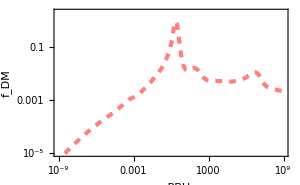

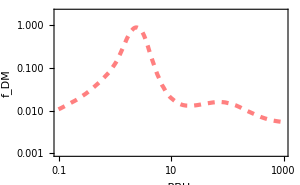

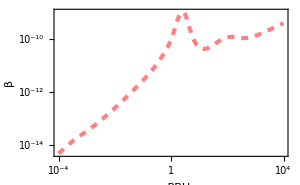

```mathematica
gamma=1.;
Amplitude=2.19 10^-2;
Subscript[n, s]=0.95;
sigmasq[mPBH_]=Amplitude (mPBH/1.)^(-(Subscript[n, s]-1)/2);
betaM0c[mPBH_]= Erfc[zetacr[mPBH]/Sqrt[2 sigmasq[mPBH]]]/2.;
MHeq=2.8 10^17;
betaeq[mPBH_]=(MHeq/mPBH)^(1/2)betaM0c[gamma mPBH];
fofmPBHM0c[mPBH_]=betaeq[mPBH]2/(Subscript[Ω, CDM]/(Subscript[Ω, CDM]+Subscript[Ω, b]));
fDMtot=NIntegrate[betaeq[mPBH]/mPBH,{mPBH,10^-9,10^7}]2/(Subscript[Ω, CDM]/(Subscript[Ω, CDM]+Subscript[Ω, b]))
PlotfDMlargeM0c=LogLogPlot[fofmPBHM0c[mPBH],{mPBH,10^-9,10^9},Frame-> True,PlotRange-> {10^-5,2.},FrameLabel->{"m_PBH","f_DM"},PlotStyle-> {Pink,Dashed,Thickness[0.01]},ImageSize-> 300]
PlotfDMzoomM0c=LogLogPlot[fofmPBHM0c[mPBH],{mPBH,10^-1,10^3},Frame-> True,PlotRange-> {0.001,2.},FrameLabel->{"m_PBH","f_DM"},PlotStyle-> {Pink,Dashed,Thickness[0.01]},ImageSize-> 300]
PlotbetaformM0c=LogLogPlot[betaM0c[mPBH],{mPBH,10^-4,10^4},Frame-> True,FrameLabel->{"m_PBH","β"},PlotStyle-> {Pink,Dashed,Thickness[0.01]},ImageSize-> 300]
```

```mathematica
(*gamma=1.;
Amplitude=2.17 10^-2;
Subscript[n, s]=0.975;
sigmasq[mPBH_]=Amplitude (mPBH/1.)^(-(Subscript[n, s]-1)/2);
betaM0c[mPBH_]= Erfc[zetacr[mPBH]/Sqrt[2 sigmasq[mPBH]]]/2.;
MHeq=2.8 10^17;
betaeq[mPBH_]=(MHeq/mPBH)^(1/2)betaM0c[gamma mPBH];
fofmPBHM0c[mPBH_]=betaeq[mPBH]2/(Subscript[Ω, CDM]/(Subscript[Ω, CDM]+Subscript[Ω, b]));
fDMtot=NIntegrate[betaeq[mPBH]/mPBH,{mPBH,10^-9,10^7}]2/(Subscript[Ω, CDM]/(Subscript[Ω, CDM]+Subscript[Ω, b]))
PlotfDMlargeM0c=LogLogPlot[fofmPBHM0c[mPBH],{mPBH,10^-9,10^9},Frame-> True,PlotRange-> {10^-5,2.},FrameLabel->{"m_PBH","f_DM"},PlotStyle-> {Pink,Dashed,Thickness[0.01]},ImageSize-> 300]
PlotfDMzoomM0c=LogLogPlot[fofmPBHM0c[mPBH],{mPBH,10^-1,10^3},Frame-> True,PlotRange-> {0.001,2.},FrameLabel->{"m_PBH","f_DM"},PlotStyle-> {Pink,Dashed,Thickness[0.01]},ImageSize-> 300]
PlotbetaformM0c=LogLogPlot[betaM0c[mPBH],{mPBH,10^-4,10^4},Frame-> True,FrameLabel->{"m_PBH","β"},PlotStyle-> {Pink,Dashed,Thickness[0.01]},ImageSize-> 300]*)
```

```mathematica
(*gamma=0.7;
Amplitude=0.3125 10^-1;
Subscript[n, s]=0.97;
sigmasq[mPBH_]=Amplitude (mPBH/1.)^(-(Subscript[n, s]-1)/2);
betaM0b[mPBH_]= Erfc[zetacr[mPBH]/Sqrt[2 sigmasq[mPBH]]]/2.;
MHeq=2.8 10^17;
(*betaeq[mPBH_]=(MHeq/mPBH)^(1/2)betaM0b[gamma mPBH];*)
betaeq[mPBH_]:=mPBH NIntegrate[1/Sqrt[2 Pi sigmasq[Exp[logmH]](4./9.)^2]Exp[-(gamma^(1./0.36)+zetacr[Exp[logmH]]4./9.)^2/(2 sigmasq[Exp[logmH]](4./9.)^2)](1./(0.36 Exp[logmH]))(MHeq/Exp[logmH])^(1/2),{logmH,-32.5,+31.5}(*Log[mPBH]-1.,Log[mPBH]+1.}*)];
betaeq[1.]
fofmPBHM0b[mPBH_]=betaeq[mPBH]2/(Subscript[Ω, CDM]/(Subscript[Ω, CDM]+Subscript[Ω, b]));
fDMtot=NIntegrate[betaeq[mPBH]/mPBH,{mPBH,10^-9,10^7}]2/(Subscript[Ω, CDM]/(Subscript[Ω, CDM]+Subscript[Ω, b]))
PlotfDMlargeM0b=LogLogPlot[fofmPBHM0b[mPBH],{mPBH,10^-9,10^9},Frame-> True,PlotRange-> {10^-5,2.},FrameLabel->{"m_PBH","f_DM"},PlotStyle-> {Pink,Dashed,Thickness[0.01]},ImageSize-> 300]
PlotfDMzoomM0b=LogLogPlot[fofmPBHM0b[mPBH],{mPBH,10^-1,10^3},Frame-> True,PlotRange-> {0.001,2.},FrameLabel->{"m_PBH","f_DM"},PlotStyle-> {Pink,Dashed,Thickness[0.01]},ImageSize-> 300]
PlotbetaformM0b=LogLogPlot[betaM0b[mPBH],{mPBH,10^-4,10^4},Frame-> True,FrameLabel->{"m_PBH","β"},PlotStyle-> {Pink,Dashed,Thickness[0.01]},ImageSize-> 300]*)
```

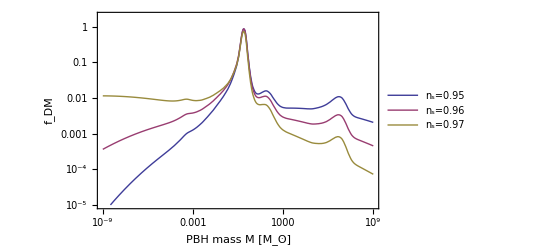

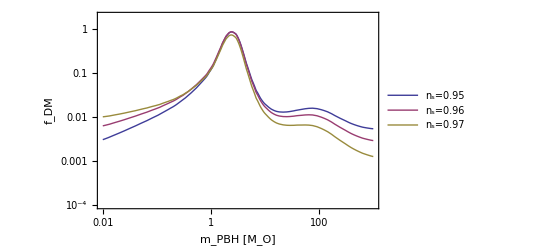

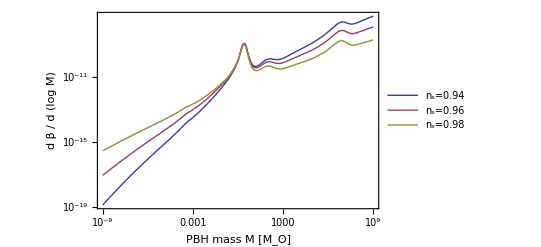

```mathematica
fDMbroad=LogLogPlot[{fofmPBHM0c[mPBH],fofmPBHM0a[mPBH],fofmPBHM0b[mPBH]},{mPBH,10^-9,10^9},Frame-> True,PlotRange-> {10^-5,2.},FrameLabel->{"PBH mass M [M_(:0298)]","f_DM"},ImageSize-> 400,PlotLegends-> Placed[{"n_s=0.95","n_s=0.96","n_s=0.97"},{0.85,0.8}]]
fDMzoom=LogLogPlot[{fofmPBHM0c[mPBH],fofmPBHM0a[mPBH],fofmPBHM0b[mPBH]},{mPBH,10^-2,10^3},Frame-> True,PlotRange-> {0.0001,2.},FrameLabel->{"m_PBH [M_(:0298)]","f_DM"},ImageSize-> 400,PlotLegends-> Placed[{"n_s=0.95","n_s=0.96","n_s=0.97"},{0.85,0.75}]]
(*fDMzoomlight=LogLogPlot[{fofmPBHM0c[mPBH],fofmPBHM0a[mPBH],fofmPBHM0b[mPBH]},{mPBH,10^-5,10^-3},Frame-> True,PlotRange-> {0.00001,2.},FrameLabel->{"m_PBH [M_(:0298)]","f_DM"},ImageSize-> 400,PlotLegends-> Placed[{"n_s=0.95","n_s=0.96","n_s=0.97"},{0.85,0.75}]]*)
betaform=LogLogPlot[{betaM0c[mPBH],betaM0a[ mPBH],betaM0b[ mPBH]},{mPBH,10^-9,10^9},Frame-> True,FrameLabel->{"PBH mass M [M_(:0298)]","d β / d (log M)"},ImageSize-> 400,PlotLegends-> Placed[{"n_s=0.94","n_s=0.96","n_s=0.98"},{0.85,0.2}]]
```

## Merging rates

```mathematica
vmean=2000.;
(*gammaPBH=0.7*)
gammaPBH=0.7 (* Ratio between PBH and Horizon masses *)
Enhfactor=10^9;
VolumeGpc=10.^27;
(*ρPBH[logmPBH_]=Subscript[ρ, CDM][1.]drhodlogMinterp[10.^logmPBH]/Normalizationbis*)
(*ρPBH[logmPBH_]=Subscript[ρ, CDM][1.]fofmPBHM0a[10.^logmPBH/gammaPBH]*)
(*ρPBH[logmPBH_]=Subscript[ρ, CDM][1.]fofmPBHM0c[10.^logmPBH/gammaPBH]*)
ρPBH[logmPBH_]=Subscript[ρ, CDM][1.]fofmPBHM0b[10.^logmPBH/gammaPBH]
nPBH[logmPBH_]=Enhfactor ρPBH[logmPBH] /msun /(10.^logmPBH)  (mpc/10.^6)^3
rate3[mPBH_,ratio_]=nPBH[Log[10,ratio  mPBH]]vmean 2.Pi(85. Pi/6./Sqrt[2.])^(2./7.)G^2(mPBH msun+ratio mPBH msun)^(10./7.)(mPBH ratio mPBH msun^2)^(2./7.)/c^4  (vmean/c)^(-18./7.)/(mpc/10.^6)^3 year;
rate[mB_,ratio_]=rate3[mB,ratio]nPBH[Log[10,mB]]VolumeGpc/Enhfactor;
Normfactor2=NIntegrate[rate[mB,ratio](mB ratio),{mB,1,50},{ratio,0.1,1.}];
finalrateM1[mB_,ratio_]=rate[mB,ratio]/(mB ratio);(*d tau / d m_heavy / d ratio *)
finalrateM1b[mB_,mA_]=rate[mB,mA/mB]/(mB mA);(*d tau / d m_A / d m_B *)
finalrateM1c[mB_,mA_]=rate[mB,mA/mB];(*d tau / d ln m_A / d ln m_B *)
Nev=NIntegrate[finalrateM1[mB,ratio],{mB,5,100.},{ratio,0.2,1.}](*/Normfactor2*)
```

0.7

1.18412×10^-18 √(10.^-logmPBH) Erfc[1/((10.^logmPBH)^0.0075)10.7222 InterpolatingFunction[{{0.0261692,0.400053}},<>][InterpolatingFunction[{{0.00053512,1.49059×10^9}},<>][1.42857 10.^logmPBH]]]

1.73947×10^10 (10.^-logmPBH)^(3/2) Erfc[1/((10.^logmPBH)^0.0075)10.7222 InterpolatingFunction[{{0.0261692,0.400053}},<>][InterpolatingFunction[{{0.00053512,1.49059×10^9}},<>][1.42857 10.^logmPBH]]]

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2776.68 and 0.0237806 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 29.5631 and 0.0000708941 for the integral and error estimates.

29.5631

## Subsolar rates

```mathematica
mmin=8.;
HighMASSrate=NIntegrate[finalrateM1[mB,ratio],{mB,mmin,80},{ratio,mmin/mB,1.}]
mmin=1.;
LowMASSrate=NIntegrate[finalrateM1[mB,ratio],{mB,mmin,5.},{ratio,mmin/mB,1.}]
Higmassmes=50.
Expectedlowmass=Higmassmes (LowMASSrate/HighMASSrate)
dmass=0.1;
dmass2=10.;
dratio=0.1;
(*ratessubsol=Table[{mB,ratio,finalrate[mB,ratio]dmass dratio Higmassmes/HighMASSrate},{mB,0.1,1.,dmass},{ratio,0.1,1,dratio}];*)
ratessubsolM1=Flatten[Table[{mB,mA,If[mA≤mB,finalrateM1[mB,mA/mB]dmass dmass/mB Higmassmes/HighMASSrate,0]},{mA,0.1,3.,dmass},{mB,0.1,3,dmass}],1];
(*ratessubsolb=Table[finalrate[mB,ratio]dmass dratio Higmassmes/HighMASSrate,{mB,0.1,1.,dmass},{ratio,0.1,1,dratio}];*)
(*ListDensityPlot[ratessubsol,PlotRange-> Full,InterpolationOrder-> 0,PlotLegends-> True]*)
PM1=ListPlot3D[ratessubsolM1,PlotRange-> {1,900},InterpolationOrder-> 0,Mesh->None,ColorFunction->"SouthwestColors",Filling->Bottom]
(*Show[PM1,BoxRatios-> {1,1,1}]*)
ratessolM1=Flatten[Table[{mB,mA,If[mA≤mB,finalrateM1[mB,mA/mB]dmass2 dmass2/mB Higmassmes/HighMASSrate,0]},{mA,10.,150.,dmass2},{mB,10.,150.,dmass2}],1];
(*ratessubsolb=Table[finalrate[mB,ratio]dmass dratio Higmassmes/HighMASSrate,{mB,0.1,1.,dmass},{ratio,0.1,1,dratio}];*)
(*ListDensityPlot[ratessubsol,PlotRange-> Full,InterpolationOrder-> 0,PlotLegends-> True]*)
(*PM2=ListPlot3D[ratessolM1,PlotRange-> {1,400},InterpolationOrder-> 0,Mesh->None,ColorFunction->"SouthwestColors",Filling->Bottom]*)
(*Show[PM1,BoxRatios-> {1,1,1}]*)
```

0.694056

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

902.774

50.

65036.1

-Graphics3D-

```mathematica
O1={{2.^(-1/5)0.2,10^6},{2.^(-1/5)0.3,4. 10^5},{2.^(-1/5)0.4,2 10^5},{2.^(-1/5)0.5,10^5},{2.^(-1/5)0.6,7 10^4},{2.^(-1/5)0.7,5 10^4},{2.^(-1/5)0.8,3 10^4},{2.^(-1/5)0.9,2.5 10^4},{2.^(-1/5),2. 10^4}}
O2={{2.^(-1/5)0.2,3.5 10^5},{2.^(-1/5)0.3,10.^5},{2.^(-1/5)0.4,5 10^4},{2.^(-1/5)0.5,3 10^4},{2.^(-1/5)0.6,2 10^4},{2.^(-1/5)0.7,1.5 10^4},{2.^(-1/5)0.8,9 10^3},{2.^(-1/5)0.9,7. 10^3},{2.^(-1/5),6. 10^3}}
ratelimitsO1=Interpolation[O1];
ratelimitsO2=Interpolation[O2];
dm=0.1;
chirp[m1_,m2_]=(m1 m2)^(3/5)/(m1+m2)^(1/5);
dchirpsq[m1_,m2_]=D[chirp[m1,m2],m1]D[chirp[m1,m2],m2]dm^2
```

{{0.17411,1000000},{0.261165,400000.},{0.34822,200000},{0.435275,100000},{0.52233,70000},{0.609385,50000},{0.69644,30000},{0.783496,25000.},{0.870551,20000.}}

{{0.17411,350000.},{0.261165,100000.},{0.34822,50000},{0.435275,30000},{0.52233,20000},{0.609385,15000.},{0.69644,9000},{0.783496,7000.},{0.870551,6000.}}

0.01 (-(m1 m2)^(3/5)/(5 (m1+m2)^(6/5))+(3 m1)/(5 (m1 m2)^(2/5) (m1+m2)^(1/5))) (-(m1 m2)^(3/5)/(5 (m1+m2)^(6/5))+(3 m2)/(5 (m1 m2)^(2/5) (m1+m2)^(1/5)))

```mathematica
dmPBH=0.01;
BigTablerates=Flatten[Table[Table[finalrateM1[mB,mA/mB]dmPBH^2/mB Higmassmes/HighMASSrate,{mB,0.2,3.,dmPBH}],{mA,0.2,1.,dmPBH}]];
BigTablechirp=Flatten[Table[Table[chirp[mA,mB],{mB,0.2,3.,dmPBH}],{mA,0.2,1.,dmPBH}]];
```

```mathematica
ratetable={};
Do[ratebin=0.;
chmass=ii 0.1/2^(1/5);
Do[If[(chmass-0.05/2^(1/5)<BigTablechirp[[jj]]≤chmass+0.05/2^(1/5)),ratebin=ratebin+BigTablerates[[jj]]],{jj,1,Length[BigTablerates]}];
ratetable=Append[ratetable,{chmass,ratebin/2.}];
Print[ratebin/2.],{ii,2,10}]
```

26.6687

220.225

664.559

1471.49

2293.89

2451.67

2433.21

2466.72

2471.25

```mathematica
totrate=Total[ratetable[[All,2]]]
psichirp=ratetable;
psichirp[[All,2]]=psichirp[[All,2]]/totrate
limitrate=Sum[O2[[ii,2]]psichirp[[ii,2]],{ii,1,9}]
```

14499.7

{0.00183926,0.0151883,0.0458326,0.101484,0.158203,0.169085,0.167811,0.170122,0.170435}

16922.8

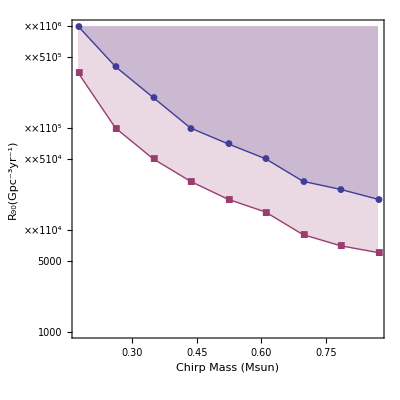

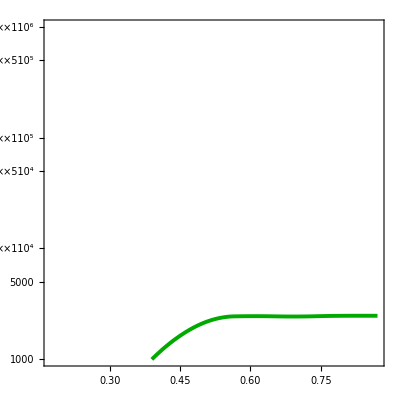

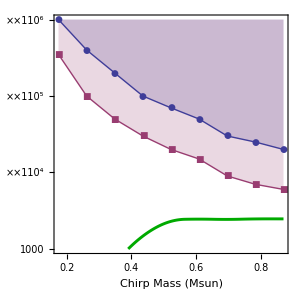

```mathematica
Plot1=ListLogPlot[{O1,O2},Joined-> True,Frame-> True,Filling-> Top,PlotRange-> {10^3,10^6},AspectRatio-> 1.,PlotMarkers-> Automatic,FrameLabel-> {"Chirp Mass (Msun)","R_90(Gpc^-3yr^-1)"}]
Plot2=ListLogPlot[ratetable,Joined-> True,Frame-> True,PlotRange-> {10^3,10^6},AspectRatio-> 1.,PlotMarkers-> None,InterpolationOrder-> 2,PlotStyle-> {Darker[Green],Thickness[0.007],Joined-> True}]
Plotfinal=Show[Plot1,Plot2,ImageSize-> 300]
```

## Mass distribution of detected events

### LIGO Noise (O2)

```mathematica
LIGOnoise=Import["~/Dropbox/PBH_dist/noise_LIGOVirgoc.dat","table"]
LIGOnoise[[All,2]]=LIGOnoise[[All,2]]Sqrt[LIGOnoise[[All,1]]]

LIGOnoiseInterp:=(Interpolation[Log[10.,LIGOnoise]])
fmax[mB_,ratio_]:=4400. /(mB(1+ratio))
```

{{10.19,4.406×10^-20},{35.735,3.059×10^-23},{52.235,1.465×10^-23},{88.085,9.779×10^-24},{135.751,8.728×10^-24},{202.502,7.608×10^-24},{297.873,8.22×10^-24},{396.119,9.24×10^-24},{551.628,1.115×10^-23},{749.339,1.36×10^-23},{1349.31,2.227×10^-23},{2253.97,3.651×10^-23},{3388.3,5.681×10^-23},{5903.12,1.115×10^-22}}

{1.40647×10^-19,1.82863×10^-22,1.05881×10^-22,9.17794×10^-23,1.01692×10^-22,1.08264×10^-22,1.41869×10^-22,1.83901×10^-22,2.61877×10^-22,3.72287×10^-22,8.18042×10^-22,1.73335×10^-21,3.30686×10^-21,8.56674×10^-21}

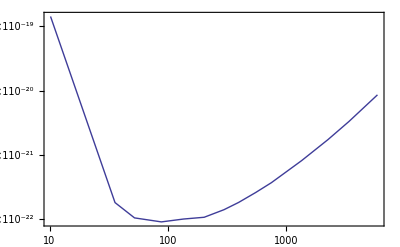

```mathematica
ListLogLogPlot[LIGOnoise,Frame-> True,Joined-> True]
```

```mathematica
sqrtSfunction=LIGOnoise(*Import["~/Dropbox/PBH_dist/noise_LIGOVirgoc.dat","table"]*)

sqrtSfunctionInterp=Interpolation[Log[10.,sqrtSfunction]]
```

{{10.19,1.40647×10^-19},{35.735,1.82863×10^-22},{52.235,1.05881×10^-22},{88.085,9.17794×10^-23},{135.751,1.01692×10^-22},{202.502,1.08264×10^-22},{297.873,1.41869×10^-22},{396.119,1.83901×10^-22},{551.628,2.61877×10^-22},{749.339,3.72287×10^-22},{1349.31,8.18042×10^-22},{2253.97,1.73335×10^-21},{3388.3,3.30686×10^-21},{5903.12,8.56674×10^-21}}

InterpolatingFunction[{{1.00817,3.77108}},<>]

```mathematica
fmax[mB_,ratio_]=2 4400. /(mB(1+ratio));
integrant=Interpolation[Table[{logfmax,Log[10.,NIntegrate[freq^(-14/6)/(10.^sqrtSfunctionInterp[Log[10,freq]])^2/10.^40,{freq,10.,10.^logfmax}]]},{logfmax,Log[10.,20.],Log[10.,2000.],0.1}],Method-> "Spline"]
integrant2[mB_,mA_]:=(mB mA/(mA+mB))^2 10.^integrant[Log[10.,Min[fmax[mB,mA/mB],2000.]]];
Rmaxcorrected[mB_,mA_]=integrant2[mB,mA]^(1/2);
(*Normfactor=NIntegrate[Rmaxcorrected[mB,ratio mB]^3,{mB,1,100},{ratio,0.1,1.}]*)
Detectability[mB_,ratio_]=Rmaxcorrected[mB,ratio mB]^3(*/Normfactor;*)
```

NIntegrate::inumr: The integrand (1.×10^-40 10.^(-2 sqrtSfunctionInterp[Log[freq]/Log[10]]))/freq^(7/3) has evaluated to non-numerical values for all sampling points in the region with boundaries {{10.,20.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::nlim: freq = 10.^logfmax is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

Interpolation::mspl: The Spline method could not be used because the data could not be coerced to machine real numbers.

NIntegrate::nlim: freq = 10.^logfmax is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

InterpolatingFunction[…]

NIntegrate::nlim: freq = 10.^logfmax is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::nlim: freq = 10.^logfmax is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::nlim: freq = 10.^logfmax is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

((10.^(InterpolatingFunction[…][0.434294 Log[Min[2000.,8800./(mB (1+ratio))]]]) mB^4 ratio^2)/(mB+mB ratio)^2)^(3/2)

```mathematica
Plot3D[Rmaxcorrected[mB,ratio mB],{mB,10,200.},{ratio,0.1,1.},PlotRange-> Full]
```

-Graphics3D-

```mathematica
Plot3D[Detectability[mB,ratio],{mB,10,150.},{ratio,0.1,1.},PlotRange-> Full]
```

-Graphics3D-

```mathematica
Eventlikd[mB_,mA_]=finalrateM1c[mB,mA] Detectability[mB,mA/mB];
(*Eventlikd[mB_,mA_]=finalrateM1c[mB,mA] Detectability[mB^(1.3),mA/mB]*)
```

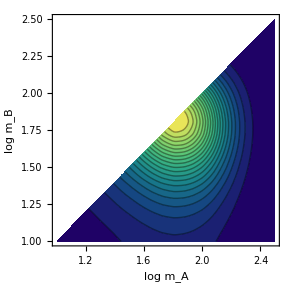

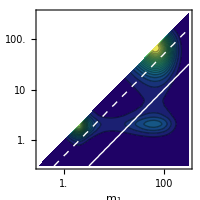

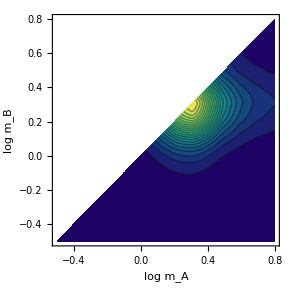

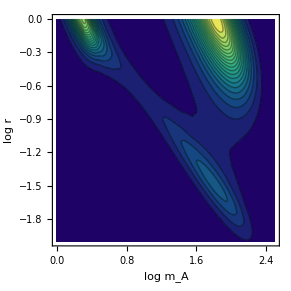

```mathematica
liksurfaceplotb=ContourPlot[{Eventlikd[10.^logmB,10.^logmA]},{logmB,1.,2.5},{logmA,1.,2.5},PlotRange-> Full, ColorFunction-> "BlueGreenYellow",Contours-> 20,FrameLabel-> {"log m_A","log m_B"},RegionFunction->Function[{logmB,logmA},logmB>logmA]]

liksurfaceplotb=Show[{ContourPlot[{Eventlikd[10.^logmB,10.^logmA]},{logmB,-0.5,2.5},{logmA,-0.5,2.5},PlotRange-> Full, ColorFunction-> "BlueGreenYellow",Contours-> 20,FrameLabel-> {"m_1","m_2"},RegionFunction->Function[{logmB,logmA},logmB>logmA],PlotRangePadding->None,FrameTicks->{{{0.,1.},{1.,10},{2.,100}},{{0.,1.},{1.,10},{2.,100.}},{{0.,""},{1.,""},{2.,""}},{{0.,""},{1.,""},{2.,""}}},ImageSize-> 200],ContourPlot[0.1 10.^logmB== 10.^logmA,{logmB,-0.5,2.5},{logmA,-0.5,2.5},ContourStyle-> White],ContourPlot[0.5 10.^logmB== 10.^logmA,{logmB,-0.5,2.5},{logmA,-0.5,2.5},ContourStyle-> {White,Dashed}](*,
ContourPlot[logmB== 0.,{logmB,-0.5,2.5},{logmA,-0.5,2.5},ContourStyle-> {Red}],
ContourPlot[10.^logmB== 2.,{logmB,-0.5,2.5},{logmA,-0.5,2.5},ContourStyle-> {Red},RegionFunction->Function[{logmB,logmA},logmB>logmA]],
ContourPlot[10.^logmB== 5.,{logmB,-0.5,2.5},{logmA,-0.5,2.5},ContourStyle-> {Red},RegionFunction->Function[{logmB,logmA},logmB>logmA]],
ContourPlot[10.^logmB== 50.,{logmB,-0.5,2.5},{logmA,-0.5,2.5},ContourStyle-> {Red},RegionFunction->Function[{logmB,logmA},logmB>logmA]]*)}]
liksurfaceplotb=ContourPlot[{Eventlikd[10.^logmB,10.^logmA]},{logmB,-0.5,0.8},{logmA,-0.5,0.8},PlotRange-> Full, ColorFunction-> "BlueGreenYellow",Contours-> 20,FrameLabel-> {"log m_A","log m_B"},RegionFunction->Function[{logmB,logmA},logmB>logmA]]
liksurfaceplotb=ContourPlot[{Eventlikd[10.^logmB,10.^(logr) 10^(logmB)]},{logmB,0.,2.5},{logr,-2.,0.},PlotRange-> Full, ColorFunction-> "BlueGreenYellow",Contours-> 20,FrameLabel-> {"log m_A","log r"},RegionFunction->Function[{logmB,logmA},logmB>logmA]]
```

```mathematica
Fig3 = Table[Eventlikd[10.^logmB,10.^logmA],{logmB,-0.5,2.5},{logmA,-0.5,2.5}]
```

{{Eventlikd[0.316228,0.316228],Eventlikd[0.316228,3.16228],Eventlikd[0.316228,31.6228],Eventlikd[0.316228,316.228]},{Eventlikd[3.16228,0.316228],Eventlikd[3.16228,3.16228],Eventlikd[3.16228,31.6228],Eventlikd[3.16228,316.228]},{Eventlikd[31.6228,0.316228],Eventlikd[31.6228,3.16228],Eventlikd[31.6228,31.6228],Eventlikd[31.6228,316.228]},{Eventlikd[316.228,0.316228],Eventlikd[316.228,3.16228],Eventlikd[316.228,31.6228],Eventlikd[316.228,316.228]}}

```mathematica
Export["Fig3_values.txt", Fig3]
```

Fig3_values.txt

```mathematica
SystemOpen["Fig3_values.txt"]
```